```mathematica
Nt = 455;(*151*)
ti = 0; tf =5; 
deltat = (tf - ti) /Nt ;
Nx = 455; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = -40; xf = 40;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax^2)//N
k = .;
j  = .;
```

0.355469

```mathematica
deltax
```

16/91

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- x^2+ⅈ x);

selectwidth = 3;
diffOrder = 4;
deriv = 2;
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
(*D1 = N[(2π)/(xf-xi)Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = deltat N[MatrixPower[D1,2],32];*)
```

```mathematica
L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->diffOrder, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
(*DL2 = N[Table[L2[[i]] * (deltat)^(i),{i,2,8}],32];*)
DL2 = L2[[2]] * deltat * (ⅈ / 2);
DL4 = L2[[4]] * (deltat * (ⅈ / 2))^2;
DL6 = L2[[6]] * (deltat * (ⅈ / 2))^3;
DL8 = L2[[8]] * (deltat * (ⅈ / 2))^4;
```

```mathematica
(*LD4*)
ULD4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD4[[1,All]] = N[f[Xo],32];
ULD4 = N[ULD4,32];
ULD4 = Chop[ULD4, 10^(-307)];
ULD4 = Developer`ToPackedArray[ULD4, Complex]; 
Developer`PackedArrayQ[ULD4]


I1 = N[IdentityMatrix[Length[DL2[[2]]]],32];
A = N[I1-DL2/2  + DL4/12,32];
B =  N[I1+DL2/2  + DL4/12,32];
MLD4 = N[Inverse[A].B,32];
EMLD4 = N[MLD4 - I1,32];
EMLD4 = Developer`ToPackedArray[EMLD4, Complex]; 
Developer`PackedArrayQ[EMLD4]

Do[ULD4[[n+1,All]] = ULD4[[n,All]] + (EMLD4 ).ULD4[[n,All]], {n,1,Nt - 1 }];
```

True

True

```mathematica
Dimensions[DL2[[2]]]
```

{455}

```mathematica
(*RK2*)
(*URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[Xo],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Complex]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[D1]],32];

MRK2 = N[(IRK2 + (ⅈ D2 / 2) - ((1/2)*(D4/4))) -  ((1/6) * (ⅈ D6 / 8)),32];
EMRK2 = N[MRK2 - IRK2,32];

EMRK2= Developer`ToPackedArray[EMRK2, Complex]; 
Developer`PackedArrayQ[EMRK2]

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]*)
```

```mathematica
(*Partial Inversion*)
```

```mathematica
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP[[1,All]] = N[f[Xo],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Complex]; 
Developer`PackedArrayQ[UP]
```

True

```mathematica
Subscript[δ, i_,j_]:=KroneckerDelta[i,j];


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[2],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder - 2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/48 ].(IP+(ⅈ * LPX)/4- LPX2/48));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n-1 )]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n-1)]]  ,{n,1,selectwidth }],{i,1,Nx},{j,1,Nx}]//MatrixForm*)

MP = N[MP//.{N[r -> deltat / (deltax)^2,32]},32];

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]], {n,1,Nt - 1 }];
```

```mathematica
(*Now we don't need D1 or DL to have 32 digit accuracy so can put it into a packed array*)
D1 = Developer`ToPackedArray[D1, Real];
D2=Developer`ToPackedArray[D2/deltat,Real];
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD4*)
FLD4 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD4 = Developer`ToPackedArray[FLD4, Real];
intLD4 = Table[0,{i,1,Length[FLD4[[All,1]]]}];
intLD4 = Developer`ToPackedArray[intLD4, Real];
GLD4 = Table[0,{i,1,Nt},{j,1,Nx}];
GLD4 = Developer`ToPackedArray[GLD4, Real];
GintLD4 = Table[0,{i,1,Length[FLD4[[All,1]]]}];
GintLD4 = Developer`ToPackedArray[GintLD4, Real];
Do[
FLD4[[i]] = Conjugate[ULD4[[i,All]]](ULD4[[i,All]])//Re;

intLD4[[i]] = (2π)/Nx Total[FLD4[[i,All]]];
GLD4[[i]] = -0.5Conjugate[ULD4[[i,All]]](L2[[2]].ULD4[[i,All]])//Re;

GintLD4[[i]] = (2π)/Nx Total[GLD4[[i,All]]]
,{i,1,Length[FLD4[[All,1]]]}];
```

```mathematica
(*RK2*)
(*FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
GRK2= Table[0,{i,1,Nt},{j,1,Nx}];
GRK2 = Developer`ToPackedArray[GRK2, Real];
GintRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
GintRK2 = Developer`ToPackedArray[GintRK2, Real];
Do[
FRK2[[i]] = Conjugate[URK2[[i,All]]](URK2[[i,All]])//Re;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]];
GRK2[[i,All]] =-0.5 Conjugate[URK2[[i,All]]](D2.URK2[[i,All]])//Re;

GintRK2[[i]] = (2π)/Nx Total[GRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)*)
```

```mathematica
(*Partial Inversion*)
FP= Table[0,{i,1,Nt},{j,1,Nx}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
GP= Table[0,{i,1,Nt},{j,1,Nx}];
GP = Developer`ToPackedArray[GP, Real];
GintP = Table[0,{i,1,Length[FP[[All,1]]]}];
GintP = Developer`ToPackedArray[GintP, Real];
Do[
FP[[i]] = Conjugate[UP[[i,All]]](UP[[i,All]])//Re;

intP[[i]] = (2π)/Nx Total[FP[[i,All]]];
GP[[i,All]] =-0.5 Conjugate[UP[[i,All]]](L2[[2]].UP[[i,All]])//Re;

GintP[[i]] = (2π)/Nx Total[GP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];
```

```mathematica
probErrorLD2=Abs[GintLD4-GintLD4[[1]]];
(*probErrorRK2=Abs[GintRK2-GintRK2[[1]]];*)
probErrorP = Abs[GintP - GintP[[1]]];
```

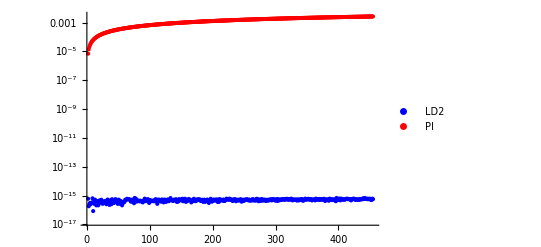

```mathematica
ListLogPlot[{probErrorLD2,probErrorP},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"}]
```

```mathematica
energyErrorLD2 = Abs[intLD4 - intLD4[[1]]];
(*energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];*)
energyErrorP = Abs[intP - intP[[1]]];
```

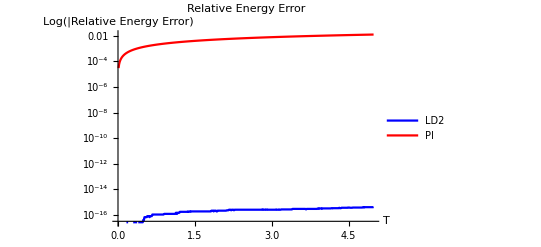

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorP}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorP]}},Joined->True]
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = 1/(√(1+2 ⅈ t))Exp[(-(x-ⅈ/2)^2)/(1+2ⅈ t)-1/4];
Uexact = Table[fexact[T[[i]],Xo[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Complex];
```

```mathematica
exacti={Re[fexact[0,Xo]],Im[fexact[0,Xo]]}//Transpose;
```

```mathematica
exactf={Re[fexact[T[[-1]],Xo]],Im[fexact[T[[-1]],Xo]]}//Transpose;
```

```mathematica
(*LD2*)
abserrLD2 = Abs[ULD4-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
(*abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];*)
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*Partial Inversion*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];
```

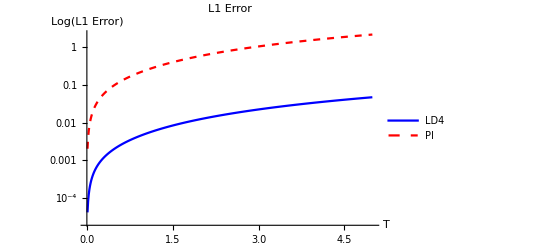

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorP}]},PlotRange->{{ti,tf},All}, PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"LD4","PI"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"L1 Error", Joined->True]
```

```mathematica
(*Animate[ListPlot[Table[ULD4[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->All], {n,0,Nt - 1,1}, AnimationRunning->False]*)
```